```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

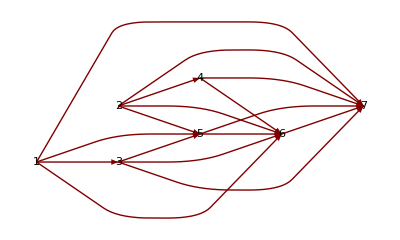

```mathematica
LayeredGraphPlot[({{0, 0, 1, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1}}),Left,AspectRatio->0.6,VertexLabeling->True]
```

```mathematica
LayeredGraphPlot[({{0, 1, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1}}),Left,AspectRatio->0.6,VertexLabeling->True,GraphHighlight->{1->2,2->5,5->6,6->7}]
```

LayeredGraphPlot::optx: Unknown option GraphHighlight in LayeredGraphPlot[{{0, 1, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1}}, Left, AspectRatio → 0.6, VertexLabeling → True, GraphHighlight → {1 → 2, 2 → 5, 5 → 6, 6 → 7}].

General::stop: Further output of LayeredGraphPlot :: optx will be suppressed during this calculation.

LayeredGraphPlot[{{0,1,0,0,1,1,1},{0,0,0,0,1,1,1},{0,0,0,1,1,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1}},Left,AspectRatio→0.6,VertexLabeling→True,GraphHighlight→{1→2,2→5,5→6,6→7}]

```mathematica
Eigensystem[({{0, 1, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1}})]
```

{{1,0,0,0,0,0,0},{{8,4,6,2,2,1,1},{0,0,1,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}}